```mathematica
S={{0,1/2,0,0},{1/3,0,0,1/2},{1/3,0,1,1/2},{1/3,1/2,0,0}};
α=0.85;
e=Table[{1},{i,4}];
n=4;
A=α S+(1-α)/n e.Transpose[e]
```

{{0.0375,0.4625,0.0375,0.0375},{0.320833,0.0375,0.0375,0.4625},{0.320833,0.0375,0.8875,0.4625},{0.320833,0.4625,0.0375,0.0375}}

```mathematica
Eigensystem[A]
(((Inverse[IdentityMatrix[n]-α S])(1-α))/n).e//Chop
```

{{1.,0.619407,-0.425,-0.194407},{{-0.113599,-0.145785,-0.9719,-0.145785},{-0.220464,-0.32131,0.863085,-0.32131},{0.67082,-0.67082,-0.223607,0.223607},{0.837494,-0.383092,-0.0713091,-0.383092}}}

{{0.0824931},{0.105866},{0.705775},{0.105866}}

## 根据开始的初始化图建立PageRank

#### 入度表示被引用

{A→0.0711921,B→0.136313,C→0.0901766,D→0.0356512}

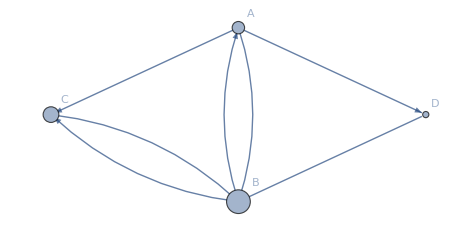

```mathematica
graphstring="ABACADBABCDBCB";
α=0.8;
pair=Partition[Characters[graphstring],2];
g=Graph[Flatten[({#[[1]]->#[[2]]})&/@pair],VertexLabels->"Name"];
Adj=AdjacencyMatrix[g];
S=Transpose[Adj].DiagonalMatrix[1/VertexOutDegree[g]];
n=VertexCount[g];
e=Table[{1},{i,n}];
A=α S+(1-α)/n e.Transpose[e];
P=(((Inverse[IdentityMatrix[n]-α S])(1-α))/n).e//Chop;
vertexSize=Thread[VertexList[g]->Flatten[P]/3]
Graph[Flatten[({#[[1]]->#[[2]]})&/@pair],VertexLabels->"Name",VertexSize->vertexSize]
```

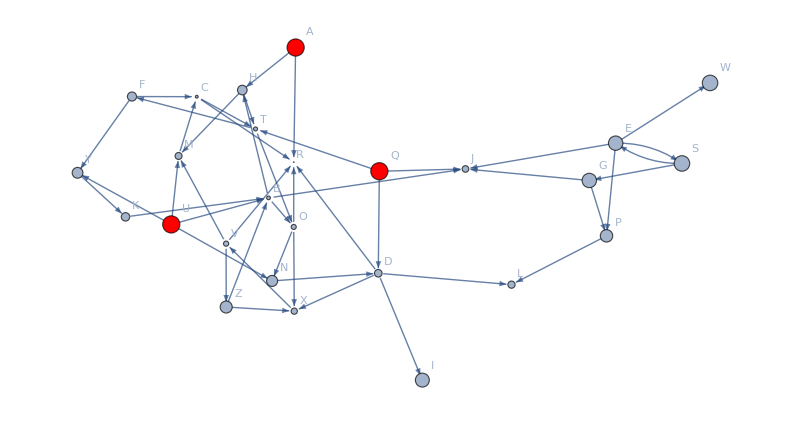

```mathematica
α=0.8;
pair=Union[Select[RandomChoice[Characters["ABCDEFGHIJKLMNOPQRSTUVWXYZ"],{50,2}],#[[1]]≠#[[2]]&]];
g=Graph[Flatten[({#[[1]]->#[[2]]})&/@pair],VertexLabels->"Name"];
Adj=AdjacencyMatrix[g];
S=Transpose[Adj].DiagonalMatrix[1/(VertexOutDegree[g]+0.0000001)];
n=VertexCount[g];
e=Table[{1},{i,n}];
A=α S+(1-α)/n e.Transpose[e];
P=(((Inverse[IdentityMatrix[n]-α S])(1-α))/n).e//Chop;
PSize=Rescale[Flatten[P],{Min[Flatten[P]],Max[Flatten[P]]},{0.05,0.01}];
mp=Max[PSize];
vertexSize=Thread[VertexList[g]->PSize];
SortBy[vertexSize,Last];
vertexstyle=(#[[1]]->Red)&/@Select[%,#[[2]]==mp&];
Graph[Flatten[({#[[1]]->#[[2]]})&/@pair],VertexLabels->"Name",VertexStyle->vertexstyle,VertexSize->((#[[1]]->n^1.6(#[[2]])^2)&/@vertexSize)]
```